# The SIR Model for Spread of Disease

## The Differential Equation Model

#### Introduction

The SIR (Susceptible-Infected-Recovered) model for the spread of infectious diseases is a very simple model of three linear differential equations. It examines how an infected population spreads a disease to a susceptible population which transforms into a recovered population.

This model assumes no one dies from the disease and that the population is also isolated and stable (no new people arrive by birth or migration during the model simulation).

#### The independent & dependent variables

In this model, the independent variable is t (time, in days):

```mathematica
Clear[t]
```

The dependent variables are S (number of susceptible individuals, at time t), I (number of infected individuals, at time t), and R (number of recovered individuals, at time t).

To simplify the differential equations we will use the scaled versions of the S, I, and R variables. The scaled variables are s, i, and r. The scale runs from 0 (representing a zero population) to 1 (representing the full population).

```mathematica
Clear[s,i,r]
```

The susceptible population starts near 1, with almost everyone being susceptible. It drops over time. The infected population starts with a positive small value near 0. The recovered population starts at 0, with no one having recovered. It increases over time.

At any given time s + i + r = 1, because the sum represents the full scaled population which is 1.

Each infected individual is assumed to spread its disease to b new individuals each day. If b is high the disease will spread faster.

```mathematica
Clear[b]
```

The fraction k represents the fraction of the infected population that recovers each day. For example, if the disease lasts 14 days, then k is (eventually) 1/14.

```mathematica
Clear[k]
```

#### The differential equations

The first equation describes how the susceptible population changes over time. Because we start with a susceptible population of 1 which decreases over time, we can assume the rate of change will be negative. Also the rate of change is proportional to the number of contacts b (more contacts decreases the susceptible population faster). Additionally the rate of change is proportionally related to the current susceptible and infected population (but not the recovered population):

```mathematica
equationS=
s'[t]==-b s[t] i[t]
```

s'[t]==-b i[t] s[t]

The second equation describes how the infected population changes over time. It has two terms. The first term is the same as the right hand side of the previous equation, except the sign is now positive. It represents the increase in infected population. The second term is negative because it represents the decrease of infected cases (people who recover):

```mathematica
equationI=
i'[t]==b s[t]i[t]-k i[t]
```

i'[t]==-k i[t]+b i[t] s[t]

The final equation describes how the recovered population changes over time. The right hand side is the same as the last term of the previous equation. It represents the transition of infected cases to recovered cases:

```mathematica
equationR=
r'[t]==k i[t]
```

r'[t]==k i[t]

Before solving the differential equations we need to set the parameters b and k.

Let' s assume that, on average, each infected person spreads their disease to one person every two days:

```mathematica
b=0.5
```

0.5

Here we assume that the average recovery time is 14 days, which means that, on average, 1/14th of the infected population recovers:

```mathematica
k=1/14.0
```

0.0714286

We also need initial values at t=0 for the susceptible, infected, and recovered population. We need a small non-zero value for the initial infected population, so will will set it to 0.0001. We will set the initial value for the susceptible population to 0.9999 (everyone else, who is not infected).  And we will set the initial recovered population to 0.

We pass the differential equations and the initial values to NDSolve and request a solution for t=100 days:

```mathematica
solution=NDSolve[{
equationS,
equationI,
equationR,
s[0]==0.9999,
i[0]==0.0001,
r[0]==0.0000
},{s,r,i},
{t,100}];
```

Next we get the individual solutions for S, I, and R:

```mathematica
solutionS=First[s/.solution];
solutionI=First[i/.solution];
solutionR=First[r/.solution];
```

#### Visualization

We can plot the results. Here, the blue line represents the susceptible population over time, red is infected, and green is recovered:

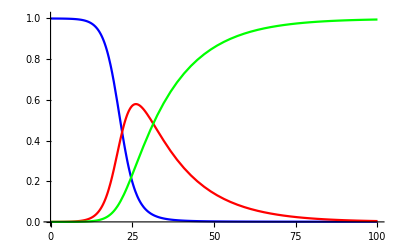

```mathematica
Plot[{
solutionS[t],
solutionI[t],
solutionR[t]
},{t,0,100},
PlotRange->{0,1.01},
PlotStyle->{Blue,Red,Green}
]
```

Alternatively we can stack these plots to highlight their sum is always 1:

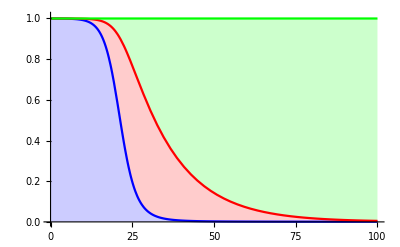

```mathematica
Plot[{
solutionS[t],
solutionS[t]+solutionI[t],
solutionS[t]+solutionI[t]+solutionR[t]
},{t,0,100},
PlotRange->{0,1.01},
Filling->{1->Axis,2->{1},3->{2}},
PlotStyle->{Blue,Red,Green}
]
```